```mathematica
α = π/4;
g = 9.8;
```

```mathematica
solutions = NDSolveValue[
{
r''[t]==(r[t] ϕ'[t]^2- g Cot[α])/Csc[α]^2,
ϕ''[t]== -(2 ϕ'[t])/r[t],
r[0] ==1,r'[0]==0,
ϕ[0]==0,ϕ'[0]==1
},
{r[t],ϕ[t]},
{t,0,1}
]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

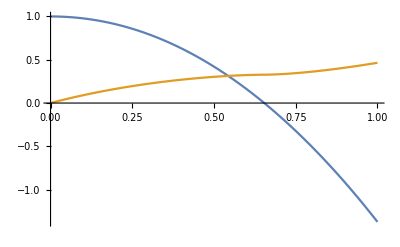

```mathematica
Plot[solutions,{t,0,1},PlotRange->All]
```

```mathematica
r[r_,ϕ_]:={r Cos[ϕ],r Sin[ϕ], r Cot[α]};
r[tp_]:=Apply[r,solutions/.t->tp];
```

```mathematica
r[0.2]
```

{0.89742,0.148872,0.909684}

```mathematica
ParametricPlot3D[r[t],{t,0,1}]
```

-Graphics3D-